Exemplo 1

ⅆy/ⅆt +1/2 y=1/2 E^(t/3)

```mathematica
sol=DSolve[y'[x]==.5 E^(x/3)-.5y[x],y[x],x]
```

{{y[x]→0.6 ⅇ^(0.333333 x)+ⅇ^(-0.5 x) C[1]}}

```mathematica
c1solve=Solve[y==sol[[1,1,2]],C[1]]
```

{{C[1]→-1. ⅇ^(0.5 x) (0.6 ⅇ^(0.333333 x)-1. y)}}

```mathematica
g[x_,y_]:=c1solve[[1,1,2]]
```

```mathematica
vectorEx1=VectorPlot[{1,.5 E^(x/3)-.5y},{x,0,6},{y,-2,4},VectorStyle->{Thin,Black,Arrowheads[0]},AspectRatio->.65];
```

```mathematica
listaConstantes=Table[ContourPlot[g[0,1]==κ,{x,0,6},{y,-2,4},ContourShading->False,ContourStyle->{Thin,Black}],{κ,-2,3,1}];
```

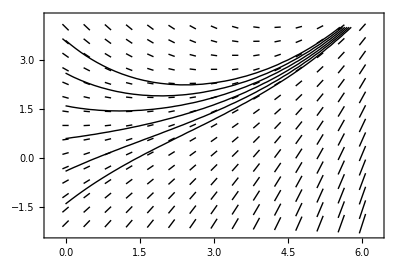

```mathematica
Show[vectorEx1,listaConstantes]
```

Exemplo 2

ⅆy/ⅆt -2y=4-t

```mathematica
sol2=DSolve[y'[x]-2y[x]==4-x,y[x],x]
```

{{y[x]→-7/4+x/2+ⅇ^(2 x) C[1]}}

```mathematica
c1solve2=Solve[y==sol2[[1,1,2]],C[1]]
```

{{C[1]→-1/4 ⅇ^(-2 x) (-7+2 x-4 y)}}

```mathematica
h[x_,y_]:=c1solve2[[1,1,2]]
```

```mathematica
vectorEx2=VectorPlot[{1,4-x+2y},{x,0,2},{y,-4,0},VectorStyle->{Thin,Black,Arrowheads[0]},AspectRatio->.65];
```

```mathematica
listaConstantes2=Table[ContourPlot[h[x,y]==κ,{x,0,2},{y,-4,0},ContourShading->False,ContourStyle->{Thin,Black}],{κ,-.7,.7,.1}];
```

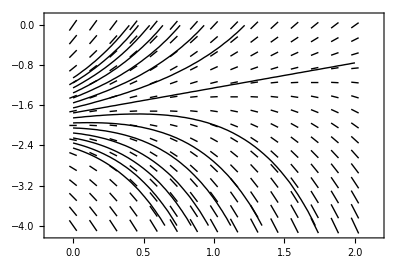

```mathematica
Show[vectorEx2,listaConstantes2]
```

Exemplo 3

PVI:   t y’ + 2 y = 4 t^2, y(1) = 2

```mathematica
Solve[t y'+2 y==4 t^2,y']
```

{{y'→(2 (2 t^2-y))/t}}

```mathematica
sol3=DSolve[x y'[x]+2y[x]==4 x^2,y[x],x]
```

{{y[x]→x^2+C[1]/x^2}}

```mathematica
c1solve3=Solve[y==sol3[[1,1,2]],C[1]]
```

{{C[1]→-x^2 (x^2-y)}}

```mathematica
i[x_,y_]=c1solve3[[1,1,2]];
```

```mathematica
contornosI=ContourPlot[i[x,y],{x,-2,2},{y,-1,3.5},ContourShading->False,Contours->20,PlotPoints->50,AspectRatio->1/2];
```

```mathematica
contorno12=ContourPlot[i[x,y]==1,{x,0,2},{y,-1,3.5},ContourStyle->{Thick,Black}];
```

```mathematica
ponto=Graphics[{PointSize[Large],Black,Point[{1,2}]}];
```

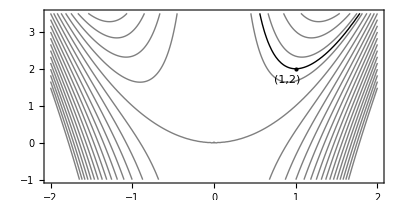

```mathematica
Show[contornosI,contorno12,ponto,Graphics[Text["(1,2)",{.9,1.7}]]]
```

Exemplo 4

PVI:  2 y’ + t y = 2, y(0) = 1

```mathematica
sol4=DSolve[2y'[x]+x y[x]==2,y[x],x]
```

{{y[x]→ⅇ^(-x^2/4) C[1]+ⅇ^(-x^2/4) √π Erfi[x/2]}}

```mathematica
c1solve4=Solve[y==sol4[[1,1,2]],C[1]]
```

{{C[1]→ⅇ^(x^2/4) y-√π Erfi[x/2]}}

```mathematica
j[x_,y_]=c1solve4[[1,1,2]];
```

```mathematica
contornosJ=Table[ContourPlot[j[x,y]==λ,{x,0,6},{y,-3,3},ContourShading->False,PlotPoints->60,AspectRatio->.65,ContourStyle->{Thin,Black}],{λ,-3,2.5,.5}];
```

```mathematica
j[0,1]
```

1

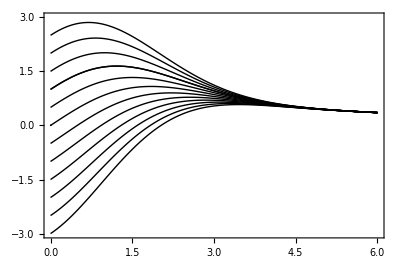

```mathematica
Show[contornosJ,ContourPlot[j[x,y]==1,{x,0,6},{y,-3,3},ContourStyle->{Black,Thick}]]
```